# Cartesian FDFD 1D wave solver discretization

He we discretize in Cartesian coordinates the 1D vector wave equation for plasmas. This is the simplest finite difference discretization you might think of. O(h^2) central difference, uniform grid h.

∇x∇xE - ω^2/c^2 * ϵ.E = iωμ_0J_A

```mathematica
ClearAll["Global`*"]
LHS[E_]:=Simplify[(T1[E*ExpVar]+T2[E*ExpVar])/ExpVar];
T1[E_]:=Simplify[Curl[Curl[E,{x,y,z}],{x,y,z}]];
T2[E_]:=-k0^2 Dot[eps,E];
eps={{exx,exy,exz},{eyx,eyy,eyz},{ezx,ezy,ezz}};
ExpVar=Exp[I(ky*y+kz*z)];
E1={Ex[x],Ey[x],Ez[x]};
LHS[E1]
CentralDiff=LHS[E1]/.{D[E_[x], x,x]->(Subscript[E, "i-1"]-2 Subscript[E, "i"]+Subscript[E, "i+1"])/(h^2),D[E_[x], x]->(-Subscript[E, "i-1"]+Subscript[E, "i+1"])/(2h),E_[x]->Subscript[E, "i"]};
Coeffs=Collect[CentralDiff,{Subscript[Ex, "i-1"],Subscript[Ex, "i"],Subscript[Ex, "i+1"],Subscript[Ey, "i-1"],Subscript[Ey, "i"],Subscript[Ey, "i+1"],Subscript[Ez, "i-1"],Subscript[Ez, "i"],Subscript[Ez, "i+1"]}]
(*Collect[Simplify[Coeffs[[1]] 2 h],{Subscript[Ex, "i-1"],Subscript[Ex, "i"],Subscript[Ex, "i+1"],Subscript[Ey, "i-1"],Subscript[Ey, "i"],Subscript[Ey, "i+1"],Subscript[Ez, "i-1"],Subscript[Ez, "i"],Subscript[Ez, "i+1"]}]
Collect[Simplify[Coeffs[[2]] 2 h/(h/2)/4],{Subscript[Ex, "i-1"],Subscript[Ex, "i"],Subscript[Ex, "i+1"],Subscript[Ey, "i-1"],Subscript[Ey, "i"],Subscript[Ey, "i+1"],Subscript[Ez, "i-1"],Subscript[Ez, "i"],Subscript[Ez, "i+1"]}]
Collect[Simplify[Coeffs[[3]] 2 h],{Subscript[Ex, "i-1"],Subscript[Ex, "i"],Subscript[Ex, "i+1"],Subscript[Ey, "i-1"],Subscript[Ey, "i"],Subscript[Ey, "i+1"],Subscript[Ez, "i-1"],Subscript[Ez, "i"],Subscript[Ez, "i+1"]}]*)
```

{(-exx k0^2+ky^2+kz^2) Ex[x]-exy k0^2 Ey[x]-exz k0^2 Ez[x]+ⅈ ky Ey'[x]+ⅈ kz Ez'[x],-eyx k0^2 Ex[x]+(-eyy k0^2+kz^2) Ey[x]-eyz k0^2 Ez[x]-ky kz Ez[x]+ⅈ ky Ex'[x]-Ey''[x],-ezx k0^2 Ex[x]-(ezy k0^2+ky kz) Ey[x]-ezz k0^2 Ez[x]+ky^2 Ez[x]+ⅈ kz Ex'[x]-Ez''[x]}

{(-exx k0^2+ky^2+kz^2) Ex_i-exy k0^2 Ey_i-(ⅈ ky Ey_(i-1))/(2 h)+(ⅈ ky Ey_(i+1))/(2 h)-exz k0^2 Ez_i-(ⅈ kz Ez_(i-1))/(2 h)+(ⅈ kz Ez_(i+1))/(2 h),-eyx k0^2 Ex_i-(ⅈ ky Ex_(i-1))/(2 h)+(ⅈ ky Ex_(i+1))/(2 h)+(2/h^2-eyy k0^2+kz^2) Ey_i-(Ey_(i-1))/h^2-(Ey_(i+1))/h^2+(-eyz k0^2-ky kz) Ez_i,-ezx k0^2 Ex_i-(ⅈ kz Ex_(i-1))/(2 h)+(ⅈ kz Ex_(i+1))/(2 h)+(-ezy k0^2-ky kz) Ey_i+(2/h^2-ezz k0^2+ky^2) Ez_i-(Ez_(i-1))/h^2-(Ez_(i+1))/h^2}

Create an analytic solution and corresponding source term using the method of manufactured solutions ...

{ⅇ^(5 ⅈ π x),ⅇ^(5 ⅈ π x),0.01 ⅇ^(5 ⅈ π x)}

{-0.00551074 ⅇ^(5 ⅈ π x),246.735 ⅇ^(5 ⅈ π x),2.46735 ⅇ^(5 ⅈ π x)}

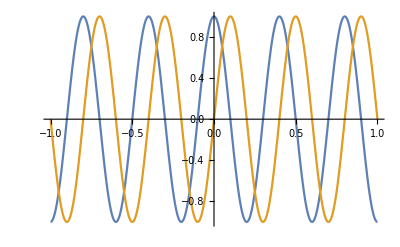

-Graphics-

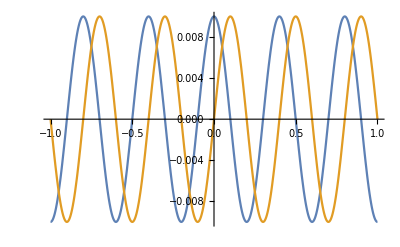

```mathematica
u={Ex,Ey, Ez }*Exp[I(kx x)];
exx=1;exy=0;exz=0;
eyx=0;eyy=1;eyz=0;
ezx=0;ezy=0;ezz=1;
xMax=1;xMin=-1;
nLambda=5;
lambda = (xMax-xMin)/nLambda;
kx = 2 Pi / lambda;
ky=0;
kz=0;
f=13 10^6;
w=2 Pi f;
c=2.99792458 10^8;
k0=w^2/c^2;
Ex = 1;Ey=1;Ez=0.01;
u
S=LHS[u]
Plot[{Re[u][[1]],Im[u][[1]]},{x,xMin,xMax}]
Plot[{Re[u][[2]],Im[u][[2]]},{x,xMin,xMax}]
Plot[{Re[u][[3]],Im[u][[3]]},{x,xMin,xMax}]
```